# NFBifurcation

```mathematica
Clear[x,μ,g,t]
```

Input the RHS of the ODE

```mathematica
f[x_,μ_] = μ*(1-x^2)+x(*1 + μ*x + x^2*)(*((μ-1)x-x^3)(μ+2-(x+1)^2)*)(*μ - x^2*)(*-x(x^2 - 2x - μ)*)
```

x+(1-x^2) μ

Find the equilibrium solutions . (Watch out for bad equilibrium solutions )

```mathematica
eqs = Solve[f[x,μ] == 0, x]
```

{{x→(1-√(1+4 μ^2))/(2 μ)},{x→(1+√(1+4 μ^2))/(2 μ)}}

Assuming that   and expanding to obtain

```mathematica
g[x0_] = Simplify[x1[t]*D[f[x0,μ],x0]]
```

(1-2 x0 μ) x1[t]

Get a list of s for each  value

```mathematica
gs[x1_,t_,μ_] = Map[g, x /. eqs];

MatrixForm[Transpose[gs[x1,t,μ]]]
```

(√(1+4 μ^2) x1[t]
-√(1+4 μ^2) x1[t])

Solve each of the  equations and determine for what values of  the solutions are stable and unstable

```mathematica
MatrixForm[FullSimplify[DSolve[ #==D[x1[t],t],x1[t],t] &/@ gs[x1,t,μ]]] (*optionary*)
```

((x1[t]→ⅇ^(t √(1+4 μ^2)) C[1])
(x1[t]→ⅇ^(-t √(1+4 μ^2)) C[1]))

Find the stable values of

```mathematica
stable = Reduce[Coefficient[#,x1[t],1] < 0, μ] &/@ gs[x1,t,μ]
unstable = Reduce[Coefficient[#,x1[t],1] > 0, μ] &/@ gs[x1,t,μ]
```

{False,μ∈ℝ}

{μ∈ℝ,False}

Let’s take a peek at whats going on

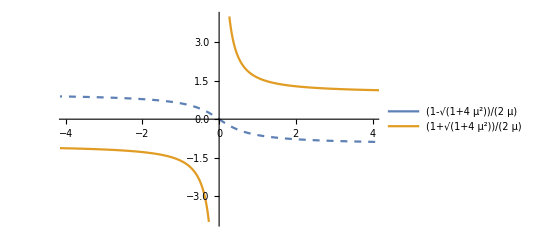

```mathematica
list = x /. eqs;
Show[Plot[
	{
	ConditionalExpression[list[[#]], stable[[#]]]==0,
	ConditionalExpression[list[[#]], unstable[[#]]]==0
	}, 
	{μ,-5,5},
	PlotRange->{{-4,4},{-4,4}},
	PlotLegends->{ToString[list[[#]],StandardForm]},
	PlotStyle->{{Thick,ColorData[97,#]},{Dashed,ColorData[97,#]}}] &/@ Table[i,{i,Length[list]}]
	]
```

Identify where on the phase portrait a stable solution meets an unstable solutions

```mathematica
pairs = Permutations[Table[i,{i,Length[list]}],{2}];
sols = {#,Solve[list[[#[[1]]]] == list[[#[[2]]]],μ]} &/@ pairs;
B = DeleteDuplicates[If[Length[#[[2]]]==1,{list[[#[[1]][[2]]]] /. #[[2]][[1]], μ /. #[[2]][[1]]},Nothing]&/@ sols]
```

{{0,2}}

Find the normal forms by taking the smallest  value that may or may not be attached to  and the smallest μ that is not attached to 

(In the case that the bifurcation points are not found using the above method, study the transition from stable to unstable and plug in, instead of #[[1]] and #[[2]])

```mathematica
expansions = Expand[f[#[[1]] + x1, #[[2]]+μ1]] &/@ B;

MatrixForm[expansions]
MatrixForm[Collect[expansions /. {x1 -> ϵ * x, μ1 -> ϵ * μ},ϵ]]
```

(-8 x1^3+x1^4+8 x1 μ1-x1^2 μ1-12 x1^3 μ1+12 x1 μ1^2-6 x1^3 μ1^2+6 x1 μ1^3-x1^3 μ1^3+x1 μ1^4)

(8 x ϵ^2 μ-x^3 ϵ^6 μ^3+ϵ^3 (-8 x^3-x^2 μ+12 x μ^2)+ϵ^4 (x^4-12 x^3 μ+6 x μ^3)+ϵ^5 (-6 x^3 μ^2+x μ^4))

There are three forms that we are expecting to see:
A saddle-node: 
A transcritical:  
A pitchfork: